```mathematica
Clear["Global`*"]
```

```mathematica
a=2.46;(*a is given in units of 10^-10*)
γ0=3.1;
γ1=0.38;
γ2=-0.015;
γ3=0.29;
γ4=0.141;
δ=-0.0105;
Δ1=0.05;
Δ2=-0.0023;
(*γ1=0.;
γ2=0.;
γ3=0.;
γ4=0.;
δ=0.;
Δ1=0.;
Δ2=0.;*)
u[kx_,ky_]=1.+2.*Cos[0.5*kx*a]*Exp[-ⅈ*ky*a*0.5*√3];
v[kx_,ky_]=Exp[ⅈ*ky*a*√3]*u[kx,ky];
Hk[kx_,ky_]={{Δ1+Δ2,-γ0*u[kx,ky],γ4*u[kx,ky]*,γ1,0,0},{-γ0*u[kx,ky]*,Δ1+Δ2+δ,γ3*v[kx,ky],γ4*u[kx,ky]*,0.5*γ2,0},{γ4*u[kx,ky],γ3*v[kx,ky]*,-2.*Δ2,-γ0*u[kx,ky],γ4*v[kx,ky]*,γ1},{γ1,γ4*u[kx,ky],-γ0*u[kx,ky]*,-2.*Δ2,γ3*u[kx,ky],γ4*u[kx,ky]*},{0,0.5*γ2,γ4*v[kx,ky],γ3*u[kx,ky]*,Δ2-Δ1+δ,-γ0*v[kx,ky]},{0,0,γ1,γ4*u[kx,ky],-γ0*v[kx,ky]*,Δ2-Δ1}};
(*Number of bands*)
Nb=Length[Hk[kx,ky]];
```

```mathematica
μ=-0.05;(*0.065*γ0;Chemical potential. VHS is at μ=-0.052175;*)
kbT=0.0000861*1; (*Boltzmann's k × temperature*)
η=0.000001;(*Self energy*) 
δc=10.*kbT;
FDif[ϵk_]=If[Abs[μ-ϵk]<δc,1/(1+Exp[(ϵk-μ)/kbT]),UnitStep[μ-ϵk]];
δFif[ϵk_]=If[Abs[μ-ϵk]<δc,-1./kbT/(2*(1+Cosh[(ϵk-μ)/kbT])),0.];
```

```mathematica
Nk=300;(*k-mesh will have Nk^2 points, Nk>1, integer*)
StringForm["The k-mesh has `` points.",Nk^2]
Λk=1; (*A factor controlling the size of the mesh in k space*)
Δk=Λk/Nk; (*Spacing between k-points*)

b=(4π)/(√3*a); (*Magnitude of reciprocal vectors*)
b1=b*{(-√3)/2,1/2}; (*Reciprocal vectors b1,b2*)
b2=b*{(√3)/2,1/2};
lineb1=Arrow[{{0,0},b1}]; 
lineb2=Arrow[{{0,0},b2}]; 
BZcontour = Polygon[{((4π)/(3a))*{-1,0},((4π)/(3a))*{(-1)/2,(√3)/2},((4π)/(3a))*{1/2,(√3)/2},((4π)/(3a))*{1,0},((4π)/(3a))*{1/2,(-√3)/2},((4π)/(3a))*{(-1)/2,(-√3)/2}}];
kaMesh=Flatten[Table[{(j-i)*Δk*b*((√3)/2),(j+i)*Δk*b*(1/2)},{i,1,Nk,1},{j,1,Nk,1}],1]; (*k-mesh first generated by reciprocal vectors *)
kaMesh1BZ=kaMesh-TensorProduct[(1-UnitStep[kaMesh.b2])*UnitStep[kaMesh.(b1+b2)]*Floor[kaMesh.b1/b^2+0.5],b1]-TensorProduct[(1-UnitStep[kaMesh.b1])*UnitStep[kaMesh.(b1+b2)]*Floor[kaMesh.b2/b^2+0.5],b2]-TensorProduct[UnitStep[kaMesh.b1]*UnitStep[kaMesh.b2]*Floor[kaMesh.(b1+b2)/b^2+0.5],(b1+b2)]; (*Moving all k-points to 1BZ*)
(*Increasing covered area of the 1BZ*)
kaMesh1BZ=kaMesh1BZ*0.03;
(*MOVING K MESH TO K POINT*)
kaMesh1BZ=(kaMesh1BZᵀ+1.0*{(4π)/(3a),0})ᵀ;
kaMeshKpoint= kaMesh1BZ;
kaMesh1BZ=kaMesh1BZ-1*TensorProduct[UnitStep[kaMesh1BZ[[All,1]]*kaMesh1BZ[[All,2]]]*Floor[kaMesh1BZ.b2/b^2+0.5],b2]-1*TensorProduct[(1-UnitStep[kaMesh1BZ[[All,1]]*kaMesh1BZ[[All,2]]])*Floor[kaMesh1BZ.b1/b^2+0.5],b1];

qaMesh1BZKpΓK=DeleteCases[kaMesh1BZ,{kx_,ky_}/; ky≠0]; (*Defining q-path as all points with ky=0. This is K'->Γ->K *)
```

The k-mesh has 90000 points.

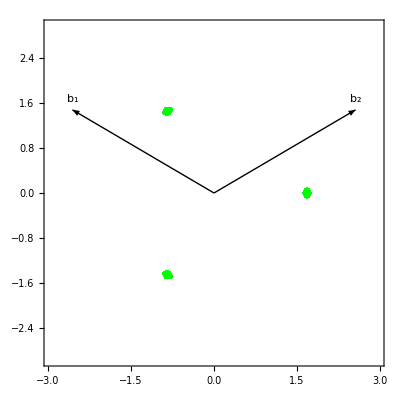

```mathematica
Show[ListPlot[{kaMesh1BZ},AspectRatio->Automatic,Epilog->{lineb1,lineb2,Text["b_1",b1+{0,0.2}],Text["b_2",b2+{0,0.2}]},AspectRatio->Automatic,PlotMarkers->{Graphics[{Green,Disk[{0,0}]}],0.01},PlotStyle->Blue,PlotRange->{{-b,b},{-b,b}},Frame->True], Graphics[{Red,Opacity[0.],EdgeForm [Dashed],BZcontour}] ]
```

-0.05

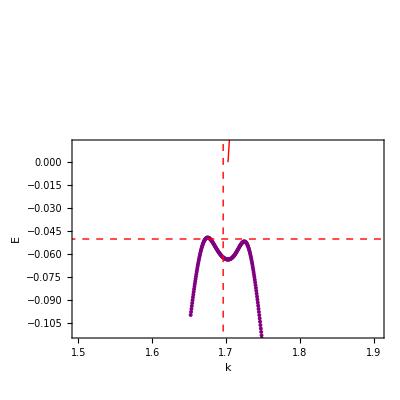

-0.055

```mathematica
Eψk=Map[Eigensystem,Apply[Hk,kaMeshKpoint,{1}]];
Enkp=Eψk[[All,1]];
(*EsurfKp=Flatten[Table[Flatten[{kaMesh1BZ[[i]],Enkp[[i,j]]}],{i,Nk^2},{j,Nb}],1];
ListPointPlot3D[EsurfKp,AspectRatio->1]
ListPlot[{kaMesh1BZ},AspectRatio->Automatic,AspectRatio->Automatic,PlotMarkers->{Graphics[{Green,Disk[{0,0}]}],0.01},PlotStyle->Blue,PlotRange->{{-ba,ba},{-ba,ba}},Frame->True]
*)
iqp=Flatten[Position[kaMeshKpoint ,{kx_,ky_} /; ky==0]];
EpathKp=Flatten[Table[Flatten[{kaMeshKpoint [[iqp[[i]]]][[1]],Enkp[[iqp[[i]],j]]}],{i,Length[iqp]},{j,Nb}],1];
EF=Line[{{-(4π)/(3a),μ},{2*(4π)/(3a),μ}}]; (*Fermi level*)
qF=Line[{{(4π)/(3.*a)+μ/(1*γ0*a),-4*γ0},{(4π)/(3.*a)+μ/(1*γ0*a),4*γ0}}];
Dirac=Line[{{(4π)/(3.*a)+0,0},{(4π)/(3.*a)+1,γ0*a*1}}];
(*To visualize μ better:
δK  = 0.3/a;
δE = 0.02*γ0;
*)
(*Fuller view *)
δK  = 0.5/a;
δE = 0.02*γ0;
k0= (4π)/(3a);
E0=μ

Show[ListPlot[EpathKp,PlotRange->{{k0-δK,k0+δK},{E0-δE,E0+δE}},Joined->False,AspectRatio->1,PlotMarkers->{Automatic, Tiny},PlotStyle->Purple,Frame->True,FrameLabel->{"k","E"}],Graphics[{Red,Dashed,EF}],Graphics[{Red,Dashed,qF}],Graphics[{Red,Thick,Dirac}],Graphics[{Red,Text[{Style["μ=",Medium],μ},{(4π)/(3a),μ+1}]}],Graphics[{Red,Text[{Style["q_F=",Medium],μ/(γ0*a)},{μ/(γ0*a)+1,4*γ0+0.5}]}]]
```

```mathematica
(*Defining parameters for sampling in q*)
Nq=100;
Lq=0.06*4;(*(4π)/(3a)*0.05;*)
Δq=Lq/Nq;

qi=Table[{0.*(-Lq/2)+i*Δq,0.},{i,0,Nq}];
ω=0.;
```

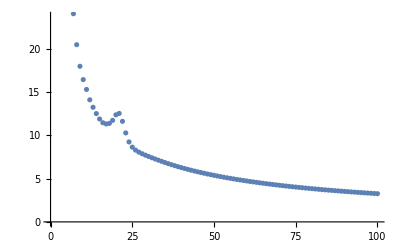

```mathematica
(*Calculating polarizability for q-path*)
Eψk=Map[Eigensystem,Apply[Hk,kaMesh1BZ,{1}]];
Enk=Eψk[[All,1]];
ψnk=Eψk[[All,2]];
ψnk=Map[Normalize,ψnk,{2}];
(*kqaMesh1BZ=kaMesh1BZ; (*Starting with q={0.,0.}*)*)
kqaMesh1BZ=(kaMesh1BZᵀ-0.0*{(4π)/(3a),0})ᵀ;(*Starting to the left of Γ*)
kqaMesh1BZ=kqaMesh1BZ-1*TensorProduct[UnitStep[kqaMesh1BZ[[All,1]]*kqaMesh1BZ[[All,2]]]*Floor[kqaMesh1BZ.b2/b^2+0.5],b2]-1*TensorProduct[(1-UnitStep[kqaMesh1BZ[[All,1]]*kqaMesh1BZ[[All,2]]])*Floor[kqaMesh1BZ.b1/b^2+0.5],b1];

Πq0=Table[0,{i,0,Nq}];
(*The q=0 point:*)
(*
Πq0[[1]] = -(2/Nk^2)*Total[Map[-1/(2*kbT*(1+Cosh[(#-μ)/kbT]))&,Enk],2];
*)
q=0.; (*Used for progress bar only*)
Monitor[
For[i=0,i≤Nq,i++,
q=i*Δq; (*Not being used*)

Eψkq=Map[Eigensystem,Apply[Hk,kqaMesh1BZ,{1}]];
Enkq= Eψkq[[All,1]];
ψnkq=Eψkq[[All,2]];
ψnkq=Map[Normalize,ψnkq,{2}];
(*
nfEk=Map[1/(1+Exp[(#-μ)/kbT])&,Enk];
nfEkq=Map[1/(1+Exp[(#-μ)/kbT])&,Enkq];

nfEk=Map[FDif[#]&,Enk,{2}];
nfEkq=Map[FDif[#]&,Enkq,{2}];
*)
nfEk=Map[UnitStep[μ-#]&,Enk,{2}];
nfEkq=Map[UnitStep[μ-#]&,Enkq,{2}];
(*if ΔE[i]=0., then make ΔE[i]=1., Δnf[i]=δf[i]. To determine which ΔE[i]=0, get indices of elements under threshold, then use those indicies to change Δnf,δf.
Position[Abs[Flatten[ΔE]],_?(# < η &)]*)
Δnf=Flatten[Table[Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,1]]-Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,2]],{i,Nk^2}]];
ΔE=Flatten[Table[Tuples[{Enk[[i]],Enkq[[i]]}][[All,1]]-Tuples[{Enk[[i]],Enkq[[i]]}][[All,2]],{i,Nk^2}]]+ω;(*+ⅈ*η*)
(*δf=Flatten[Map[-1/(2*kbT*(1+Cosh[(#-μ)/kbT]))&,Table[Tuples[{Enk[[i]],Enkq[[i]]}][[All,1]],{i,Nk^2}]]];*)
ψTuples=Table[Tuples[{ψnk[[i]],ψnkq[[i]]*}],{i,Nk^2}];
Fkq=Flatten[Table[Abs[ψTuples[[i]][[j]][[1]].ψTuples[[i]][[j]][[2]]]^2,{i,Nk^2},{j,Nb^2}]];
idiv=Flatten[Position[Abs[ΔE],_?(#==0.&)]];
ΔE[[idiv]]=1.;
(*Fkq[[idiv]]=1.;*)

(*
Δnf[[idiv]]=Map[-1/(2*kbT*(1+Cosh[(#-μ)/kbT]))&,Flatten[Table[Tuples[{Enk[[i]],Enkq[[i]]}][[All,1]],{i,Nk^2}]][[idiv]]];
*)
Δnf[[idiv]]=Map[δFif[#]&,Flatten[Table[Tuples[{Enk[[i]],Enkq[[i]]}][[All,1]],{i,Nk^2}]][[idiv]]];

Πq0[[i+1]]=-(2/Nk^2)*Total[Δnf*Re[1/ΔE]*Fkq];(**((ω)/Norm[q]^2)... -0.*η*Im[1/ΔE]*δf *)
kqaMesh = (kqaMesh1BZᵀ+{Δq,0})ᵀ;

kqaMesh1BZ = kqaMesh-1*TensorProduct[UnitStep[kqaMesh.(b1+b2)]*Floor[kqaMesh.b2/b^2+0.5],b2]-1*TensorProduct[(1-UnitStep[kqaMesh.(b1+b2)])*Floor[kqaMesh.b1/b^2+0.5],b1]
]
,Grid[{{Text[Style["Progress:",Darker[Blue,0.66]]],ProgressIndicator[q,{0.,Lq*1.05}],StringForm["``%",NumberForm[100*q/(Lq*1.05),{3,2}]]},{Text[Style["Current value of q: ",Darker[Blue,0.66]]],q ,StringForm["Final value: ``",NumberForm[Lq]] }},Alignment->Left,Dividers->Center]];
ListPlot[Table[{i,Re[Πq0[[i]]]},{i,1,Nq}]]
```

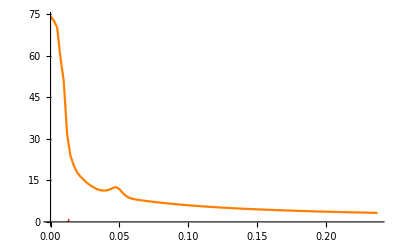

```mathematica
Show[ListPlot[Table[{qi[[i,1]],Re[Πq0[[i]]]},{i,1,Nq}], PlotRange->All,PlotStyle-> Orange,Joined->True],Graphics[{Red,Line[{{-2*μ/(γ0*a),0},{-2*1μ/(γ0*a),1}}]}]]
```

```mathematica
EmitSound[Play[Sin[10*π*t]SawtoothWave[880*2 Pi t],{t,0,0.5}]]
```

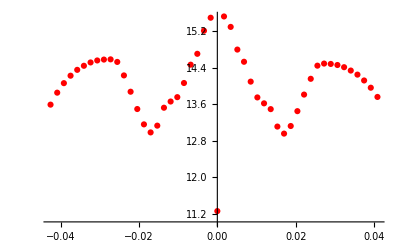

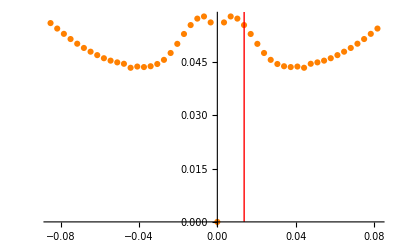
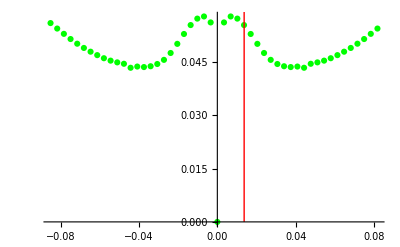
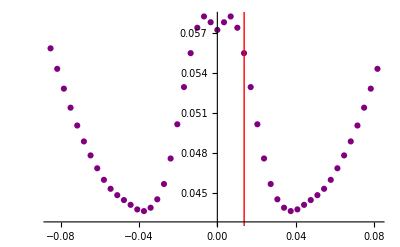
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-](*Before and after flattening before summing over k. Purple: after removing self energy from denominator. We are now subsituting δf for Abs[ΔE]<η, η=0.001,Nk=50*)
```

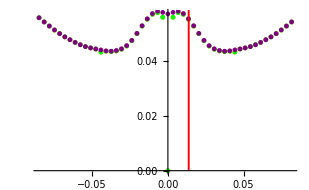

```mathematica
A={1,2,-4,6,8+ⅈ,10};
B=Abs[Re[A]]
B[[{2,5}]]={kk,qq};
B

(*Position[B,_?(#<η&)]*)
```

{1,2,4,6,8,10}

{1,kk,4,6,qq,10}

```mathematica
Enkt={{e1k1,e2k1,e3k1},{e1k2,e2k2,e3k2}};
Enkqt={{e1q1,e2q1,e3q1},{e1q2,e2q2,e3q2}};
i=2;
Tuples[{Enkt[[i]],Enkqt[[i]]}][[All,1]][[{1,4,7}]]
Tuples[{Enkt[[i]],Enkqt[[i]]}][[All,1]]-Tuples[{Enkt[[i]],Enkqt[[i]]}][[All,2]]
```

{e1k2,e2k2,e3k2}

{e1k2-e1q2,e1k2-e2q2,e1k2-e3q2,-e1q2+e2k2,e2k2-e2q2,e2k2-e3q2,-e1q2+e3k2,-e2q2+e3k2,e3k2-e3q2}

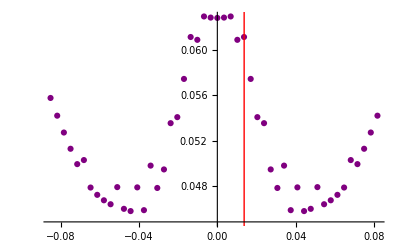
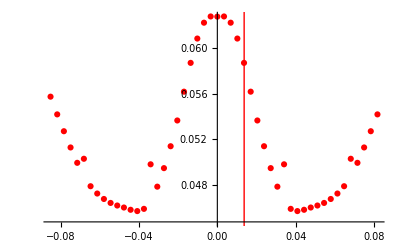
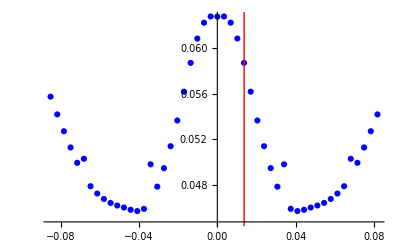
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-](*Purple: Same but for Nk=150. Red: Same but η=0.0001, this fixed the points closer to q=0*)
```

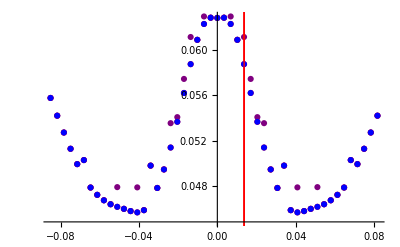

```mathematica
(*Started at pm 5/3/21*)(*calcualting same resolution but for the main cuadrant ω,q<1.25*)(**)
Monitor[Table[Pause[0.001],{ω,0.625,1.25,(1.25-0.625)/20},{q,0.01,0.625,(0.625-0.01)/20}],Grid[{{Text[Style["Progress:",Darker[Blue,0.66]]],ProgressIndicator[ω,{0.625,1.25}],StringForm["``%",NumberForm[100*(ω-0.625)/(1.25-0.625),{3,2}]]},{Text[Style["Current value of ω: ",Darker[Blue,0.66]]],ω ,StringForm["Final value: ``",NumberForm[1.25]] }},Alignment->Left,Dividers->Center]];
```

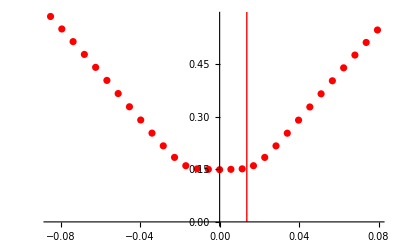
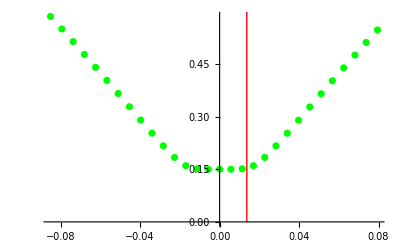
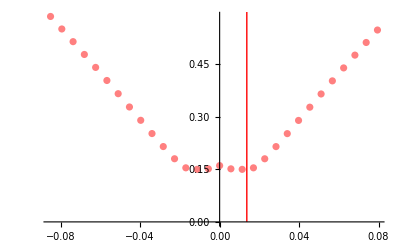
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-] (*Nk=150, kamesh*0.2, K-centered, graphene parameters. Div condition # < 0. fixed problems at q=0,q_\pm. Removed Fkq=1. it didn.b4t appear to make difference.Green: Nk=200, almost no diff., a little diff at q=0. Pink: kbT=0.05 mK (the other ones are at 0.1mK), looks flatter but seems to diverge at q=0 *)
```

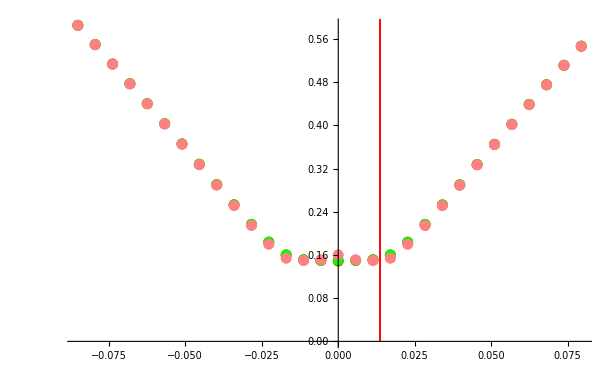

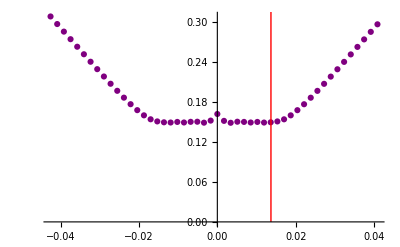
```mathematica
Show[-Graphics-](*Same but Nq=50, Lq=(4π)/(3a)*0.05*)
```

-Graphics-

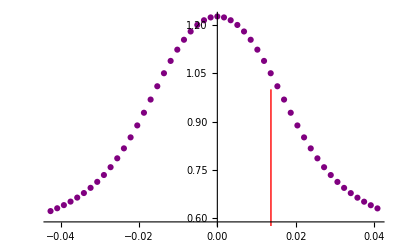
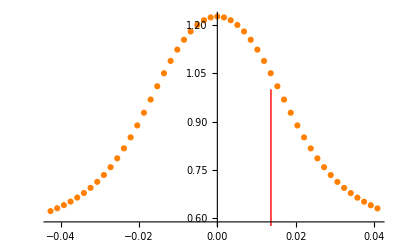
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-](*Same but for trilayer parameters, for Nk=200. Green: Nk=300 (didn't change). Yellow: kamesh*0.05. Nk=200 (didn't change), Orange: kamesh*0.2 (didnt change)*)
```

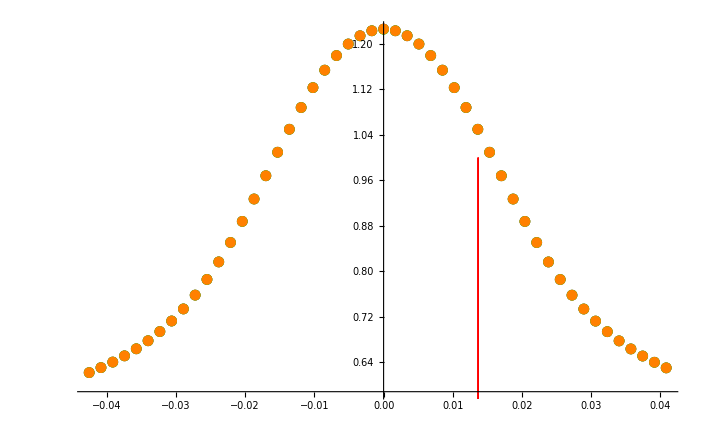

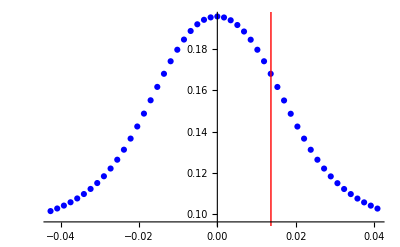
```mathematica
Show[-Graphics-](*Blue: kamesh*0.5, THE AMPLITUDE CHANGES A LOT*)
```

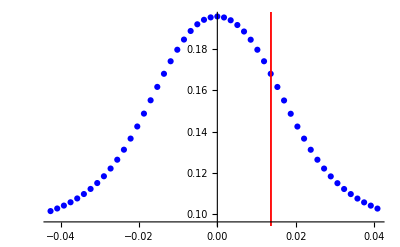

-Graphics-

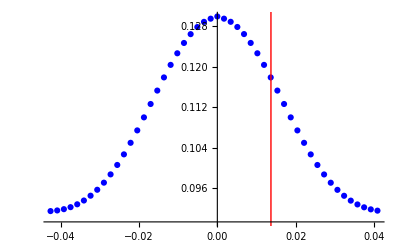
```mathematica
Show[-Graphics-] (*Green: T= 0.1mK (past plots were  at 0.05mk)*)
```

-Graphics-

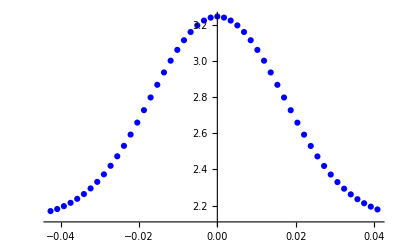
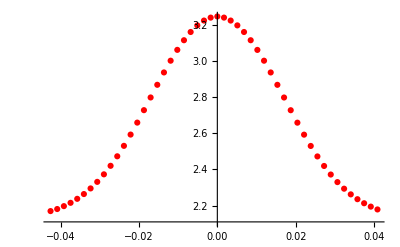
```mathematica
Show[-Graphics-,-Graphics-](*TESTING CUT FOR FD[ϵk].For Nk=50. Blue: before, Red: after. Seems to not have changed*)
```

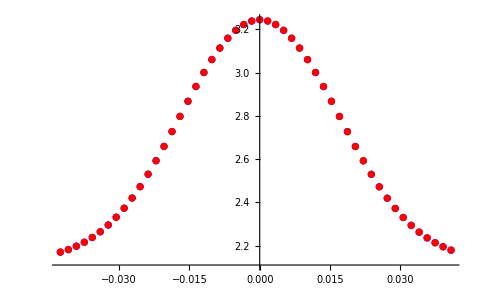

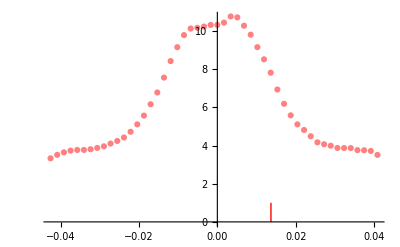
```mathematica
Show[-Graphics-] (*For T=0.01mk*)
```

-Graphics-

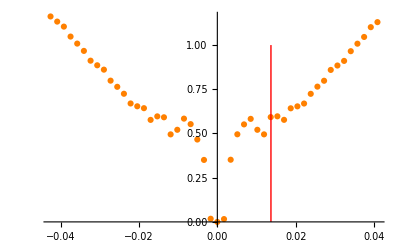
```mathematica
Show[-Graphics-] (*Graphene parameters. Nk=50, kamesh*0.05, K-centered, cut fermi distributions. T=0.01mK (now there are no errors of exponentials)*)
```

-Graphics-

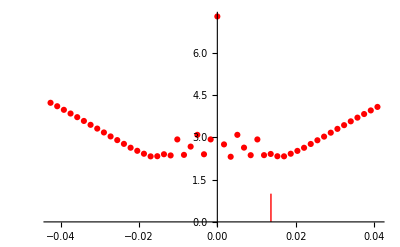
```mathematica
Show[-Graphics-](*Same but kamesh*0.05 (it got better!)*)
```

-Graphics-

```mathematica
Show[-Graphics-] (*Same but kamesh*0.02 (it got worse!)*)
```

-Graphics-

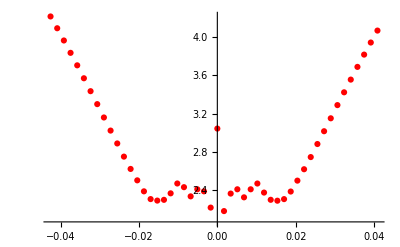
```mathematica
Show[-Graphics-](*Same but Nk=100*)
```

-Graphics-

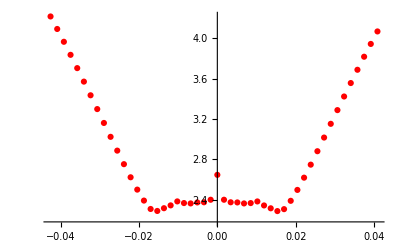
```mathematica
Show[-Graphics-] (*Nk=150*)
```

-Graphics-

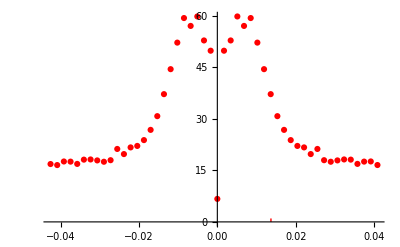
```mathematica
Show[-Graphics-](*Trilayer parameters, Nk=150, replacing FD by  UnitStep*)
```

-Graphics-

```mathematica
Show[-Graphics-](*Nk=150*)
```

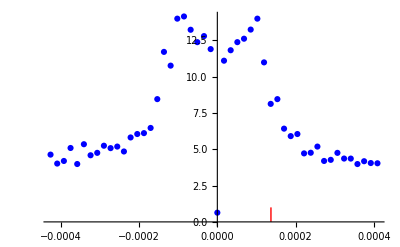
```mathematica
Show[-Graphics-](*a->s*a, s=100, T=5K*)
```

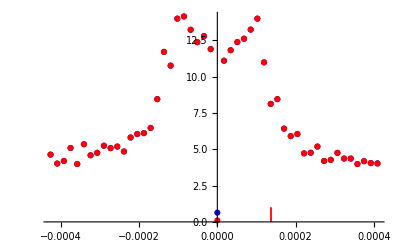

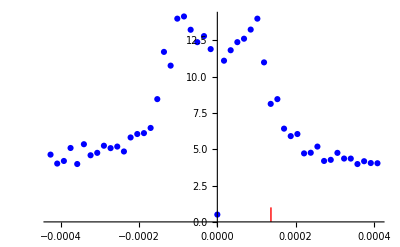
```mathematica
Show[-Graphics-](*T=10K*)
```

-Graphics-

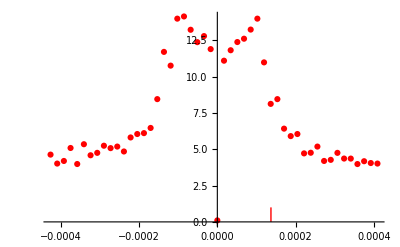
```mathematica
Show[-Graphics-] (*T=100K. Its not changing*)
```

-Graphics-

```mathematica
N[12*10^4]
```

120000.

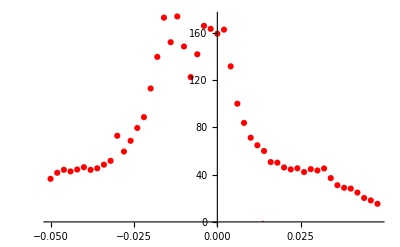
```mathematica
Show[-Graphics-] (*Trying to reproduce the results of Simplified model with realistic parameters. Nk=100, T=100K, kamesh*0.03, Lq=0.1, Nq= 50, μ=-0.052175, δc=10.*kbT. (my mistake, I didn't center on q, but maybe this is acually more accurate than I thought)*)
```

-Graphics-

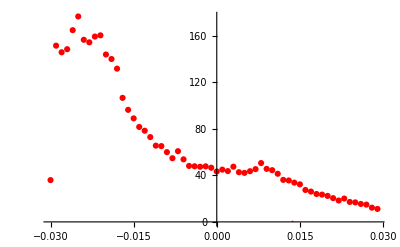
```mathematica
Show[-Graphics-] (*Nq=60, Starting at K point (instead of going through it from K-Lq/2 to K+Lq/2). Also Lq=0.06*)
```

-Graphics-

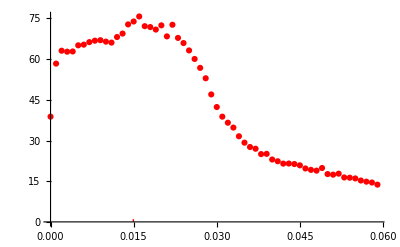
```mathematica
Show[-Graphics-] (*Same but μ=-0.57, also fixed the starting point of q path at K*)
```

-Graphics-

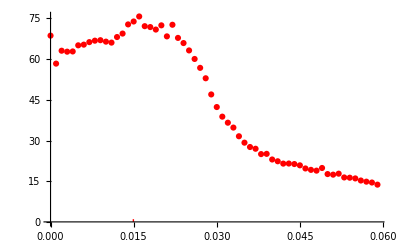
```mathematica
Show[-Graphics-] (*Same but T=10K*)
```

-Graphics-

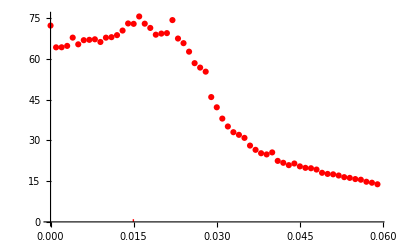
```mathematica
Show[-Graphics-] (*Same but T=1K, Nk=150. You kind of see the 3 expected peaks, 2 around 0.02 and 1 around 0.4. The ones at low q is probably noise due to low Nk,as we've seen from the simplified model*)
```

-Graphics-

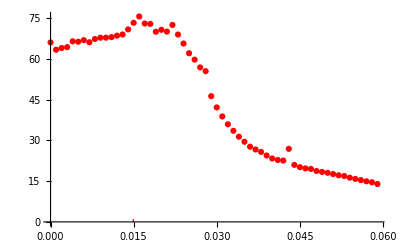
```mathematica
Show[-Graphics-](*Same but Nk=250*)
```

-Graphics-

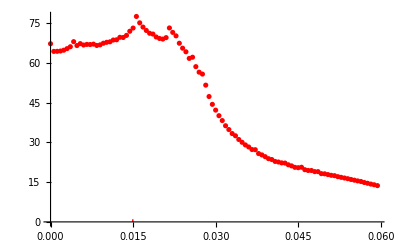
```mathematica
Show[-Graphics-] (*Same but Nk=300, Nq=100*)
```

-Graphics-

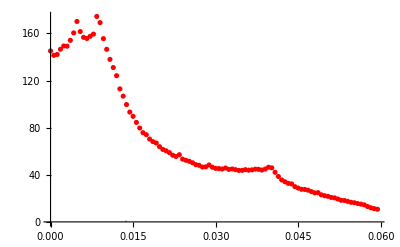
```mathematica
Show[-Graphics-] (*Same but μ at VHS*)
```

-Graphics-

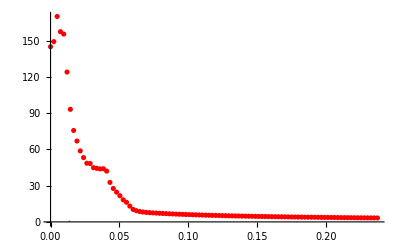
```mathematica
Show[-Graphics-](*Same but Nq=100, Lq=0.06*4*)
```

-Graphics-

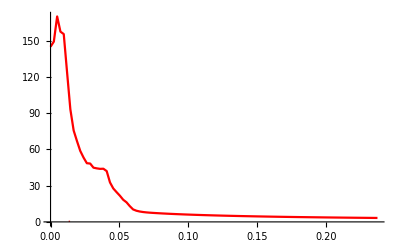
```mathematica
(*DATA*)
Show[-Graphics-]
Table[{qi[[i,1]],Re[Πq0[[i]]]},{i,1,Nq}]
```

-Graphics-

```mathematica
dataμVHS={{0.,145.06150868045785},{0.0024,149.3145748542893},{0.0048,170.12791011599455},{0.0072,157.53864460655166},{0.0096,155.53907893878136},{0.011999999999999999,124.09592502686013},{0.0144,93.2193081325244},{0.0168,75.70931583370641},{0.0192,66.9695816428422},{0.021599999999999998,58.777758258296586},{0.023999999999999997,53.24571264744643},{0.026399999999999996,48.59839464113396},{0.0288,48.32422747499152},{0.0312,44.90516760576428},{0.0336,44.3331614198124},{0.036,43.92578613051369},{0.0384,44.02183827099721},{0.040799999999999996,42.078526434143384},{0.043199999999999995,32.70449393497308},{0.045599999999999995,27.686925118849388},{0.047999999999999994,24.62042127339301},{0.05039999999999999,21.689857735960224},{0.05279999999999999,18.340295406859912},{0.05519999999999999,16.237877371532896},{0.0576,13.05338425628327},{0.06,10.333919125716658},{0.0624,9.249079339962742},{0.0648,8.60684868296063},{0.0672,8.178338289876734},{0.0696,7.874964066887173},{0.072,7.644736007443611},{0.0744,7.456811068717207},{0.0768,7.288442965105074},{0.07919999999999999,7.130784987748473},{0.08159999999999999,6.982079191926833},{0.08399999999999999,6.841353566235895},{0.08639999999999999,6.707869185366134},{0.08879999999999999,6.580992659334931},{0.09119999999999999,6.460156583095777},{0.09359999999999999,6.34484966721123},{0.09599999999999999,6.234613795238058},{0.09839999999999999,6.129041117706454},{0.10079999999999999,6.027770002457274},{0.10319999999999999,5.930480231082339},{0.10559999999999999,5.8368880140015085},{0.10799999999999998,5.746741229771648},{0.11039999999999998,5.659815105339867},{0.11279999999999998,5.575908419330679},{0.1152,5.4948402304927475},{0.1176,5.416447092261594},{0.12,5.340580697146245},{0.1224,5.267105890839125},{0.1248,5.195898999009128},{0.12719999999999998,5.126846415830821},{0.1296,5.059843410318701},{0.13199999999999998,4.994793113393265},{0.1344,4.9316056548110065},{0.13679999999999998,4.870197424468516},{0.1392,4.810490437132281},{0.14159999999999998,4.752411783418172},{0.144,4.695893152945977},{0.14639999999999997,4.640870418127467},{0.1488,4.5872832691081395},{0.15119999999999997,4.5350748920574535},{0.1536,4.484191684362294},{0.156,4.434583001383518},{0.15839999999999999,4.386200930334816},{0.1608,4.339000087576499},{0.16319999999999998,4.292937436216547},{0.1656,4.247972121402869},{0.16799999999999998,4.204065321095391},{0.1704,4.1611801104402755},{0.17279999999999998,4.119281338145391},{0.1752,4.078335513486054},{0.17759999999999998,4.03831070276209},{0.18,3.9991764341881493},{0.18239999999999998,3.960903610334471},{0.1848,3.9234644273497774},{0.18719999999999998,3.886832300294646},{0.1896,3.850981793996346},{0.19199999999999998,3.8158885589066185},{0.1944,3.7815292715042133},{0.19679999999999997,3.747881578836165},{0.1992,3.7149240468366798},{0.20159999999999997,3.682636112101591},{0.204,3.650998036830225},{0.20639999999999997,3.6199908666761553},{0.20879999999999999,3.589596391274378},{0.21119999999999997,3.5597971072351884},{0.21359999999999998,3.530576183415224},{0.21599999999999997,3.5019174282938677},{0.21839999999999998,3.4738052592991413},{0.22079999999999997,3.4462246739410887},{0.22319999999999998,3.419161222623316},{0.22559999999999997,3.392600983014422},{0.22799999999999998,3.3665305358712794},{0.2304,3.3409369422149044},{0.23279999999999998,3.315807721767979},{0.2352,3.2911308325702864},{0.23759999999999998,3.2668946516950346}}
```

{{0.,145.062},{0.0024,149.315},{0.0048,170.128},{0.0072,157.539},{0.0096,155.539},{0.012,124.096},{0.0144,93.2193},{0.0168,75.7093},{0.0192,66.9696},{0.0216,58.7778},{0.024,53.2457},{0.0264,48.5984},{0.0288,48.3242},{0.0312,44.9052},{0.0336,44.3332},{0.036,43.9258},{0.0384,44.0218},{0.0408,42.0785},{0.0432,32.7045},{0.0456,27.6869},{0.048,24.6204},{0.0504,21.6899},{0.0528,18.3403},{0.0552,16.2379},{0.0576,13.0534},{0.06,10.3339},{0.0624,9.24908},{0.0648,8.60685},{0.0672,8.17834},{0.0696,7.87496},{0.072,7.64474},{0.0744,7.45681},{0.0768,7.28844},{0.0792,7.13078},{0.0816,6.98208},{0.084,6.84135},{0.0864,6.70787},{0.0888,6.58099},{0.0912,6.46016},{0.0936,6.34485},{0.096,6.23461},{0.0984,6.12904},{0.1008,6.02777},{0.1032,5.93048},{0.1056,5.83689},{0.108,5.74674},{0.1104,5.65982},{0.1128,5.57591},{0.1152,5.49484},{0.1176,5.41645},{0.12,5.34058},{0.1224,5.26711},{0.1248,5.1959},{0.1272,5.12685},{0.1296,5.05984},{0.132,4.99479},{0.1344,4.93161},{0.1368,4.8702},{0.1392,4.81049},{0.1416,4.75241},{0.144,4.69589},{0.1464,4.64087},{0.1488,4.58728},{0.1512,4.53507},{0.1536,4.48419},{0.156,4.43458},{0.1584,4.3862},{0.1608,4.339},{0.1632,4.29294},{0.1656,4.24797},{0.168,4.20407},{0.1704,4.16118},{0.1728,4.11928},{0.1752,4.07834},{0.1776,4.03831},{0.18,3.99918},{0.1824,3.9609},{0.1848,3.92346},{0.1872,3.88683},{0.1896,3.85098},{0.192,3.81589},{0.1944,3.78153},{0.1968,3.74788},{0.1992,3.71492},{0.2016,3.68264},{0.204,3.651},{0.2064,3.61999},{0.2088,3.5896},{0.2112,3.5598},{0.2136,3.53058},{0.216,3.50192},{0.2184,3.47381},{0.2208,3.44622},{0.2232,3.41916},{0.2256,3.3926},{0.228,3.36653},{0.2304,3.34094},{0.2328,3.31581},{0.2352,3.29113},{0.2376,3.26689}}

```mathematica
Show[-Graphics-] (*Same but μ=-0.51*)
dataμmp051=dataμm0p51
```

-Graphics-

{{0.,104.274},{0.0024,101.518},{0.0048,93.4826},{0.0072,89.5802},{0.0096,78.7441},{0.012,62.371},{0.0144,55.8248},{0.0168,49.5535},{0.0192,39.8907},{0.0216,33.617},{0.024,30.2071},{0.0264,27.5562},{0.0288,26.0028},{0.0312,24.9291},{0.0336,23.9397},{0.036,23.0881},{0.0384,22.1701},{0.0408,21.9642},{0.0432,24.9136},{0.0456,24.1873},{0.048,20.3491},{0.0504,16.7461},{0.0528,13.6007},{0.0552,10.9678},{0.0576,9.48285},{0.06,8.74234},{0.0624,8.3023},{0.0648,8.02197},{0.0672,7.81486},{0.0696,7.635},{0.072,7.47037},{0.0744,7.3153},{0.0768,7.16728},{0.0792,7.02538},{0.0816,6.88929},{0.084,6.75883},{0.0864,6.63385},{0.0888,6.51411},{0.0912,6.39932},{0.0936,6.2892},{0.096,6.18345},{0.0984,6.08179},{0.1008,5.98396},{0.1032,5.88971},{0.1056,5.79882},{0.108,5.71109},{0.1104,5.62633},{0.1128,5.54439},{0.1152,5.4651},{0.1176,5.38832},{0.12,5.31393},{0.1224,5.2418},{0.1248,5.17184},{0.1272,5.10393},{0.1296,5.03798},{0.132,4.97391},{0.1344,4.91163},{0.1368,4.85107},{0.1392,4.79215},{0.1416,4.7348},{0.144,4.67897},{0.1464,4.62459},{0.1488,4.57161},{0.1512,4.51997},{0.1536,4.46962},{0.156,4.42052},{0.1584,4.37261},{0.1608,4.32586},{0.1632,4.28022},{0.1656,4.23566},{0.168,4.19213},{0.1704,4.14961},{0.1728,4.10806},{0.1752,4.06744},{0.1776,4.02773},{0.18,3.98889},{0.1824,3.9509},{0.1848,3.91373},{0.1872,3.87736},{0.1896,3.84176},{0.192,3.8069},{0.1944,3.77277},{0.1968,3.73934},{0.1992,3.70659},{0.2016,3.6745},{0.204,3.64306},{0.2064,3.61224},{0.2088,3.58202},{0.2112,3.55239},{0.2136,3.52333},{0.216,3.49483},{0.2184,3.46687},{0.2208,3.43944},{0.2232,3.41252},{0.2256,3.38609},{0.228,3.36016},{0.2304,3.33469},{0.2328,3.30968},{0.2352,3.28512},{0.2376,3.261}}

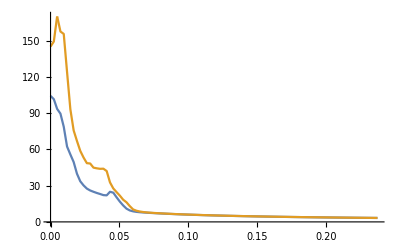

```mathematica
ListPlot[{dataμmp051,dataμVHS},Joined->True,PlotRange->{0,170}]
```

```mathematica
dataμmp05=Table[{qi[[i,1]],Re[Πq0[[i]]]},{i,1,Nq}]
```

{{0.,74.2559},{0.0024,72.7569},{0.0048,70.2896},{0.0072,59.3886},{0.0096,50.81},{0.012,31.9445},{0.0144,24.0525},{0.0168,20.4773},{0.0192,17.9838},{0.0216,16.4444},{0.024,15.307},{0.0264,14.1072},{0.0288,13.2459},{0.0312,12.517},{0.0336,11.8923},{0.036,11.4576},{0.0384,11.3216},{0.0408,11.3856},{0.0432,11.7379},{0.0456,12.3736},{0.048,12.5361},{0.0504,11.6214},{0.0528,10.2847},{0.0552,9.23886},{0.0576,8.63901},{0.06,8.29673},{0.0624,8.06514},{0.0648,7.87851},{0.0672,7.71367},{0.0696,7.56},{0.072,7.41253},{0.0744,7.26922},{0.0768,7.12956},{0.0792,6.9938},{0.0816,6.86233},{0.084,6.73544},{0.0864,6.61327},{0.0888,6.49579},{0.0912,6.38284},{0.0936,6.27425},{0.096,6.16978},{0.0984,6.06921},{0.1008,5.97231},{0.1032,5.87887},{0.1056,5.78869},{0.108,5.70158},{0.1104,5.61738},{0.1128,5.53593},{0.1152,5.45709},{0.1176,5.38071},{0.12,5.30669},{0.1224,5.2349},{0.1248,5.16524},{0.1272,5.09761},{0.1296,5.03193},{0.132,4.96809},{0.1344,4.90604},{0.1368,4.84568},{0.1392,4.78696},{0.1416,4.72979},{0.144,4.67413},{0.1464,4.61992},{0.1488,4.56708},{0.1512,4.51559},{0.1536,4.46537},{0.156,4.41639},{0.1584,4.36861},{0.1608,4.32197},{0.1632,4.27644},{0.1656,4.23199},{0.168,4.18856},{0.1704,4.14613},{0.1728,4.10467},{0.1752,4.06414},{0.1776,4.02451},{0.18,3.98575},{0.1824,3.94783},{0.1848,3.91074},{0.1872,3.87443},{0.1896,3.8389},{0.192,3.8041},{0.1944,3.77003},{0.1968,3.73666},{0.1992,3.70397},{0.2016,3.67194},{0.204,3.64054},{0.2064,3.60977},{0.2088,3.5796},{0.2112,3.55002},{0.2136,3.52101},{0.216,3.49256},{0.2184,3.46464},{0.2208,3.43725},{0.2232,3.41036},{0.2256,3.38398},{0.228,3.35808},{0.2304,3.33265},{0.2328,3.30768},{0.2352,3.28315},{0.2376,3.25907}}

```mathematica
Show[-Graphics-](*Same but μ=-0.05*)
```

-Graphics-

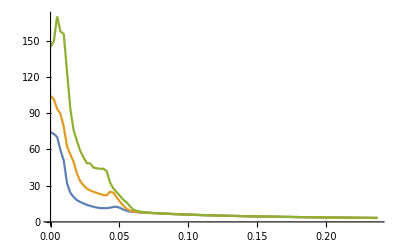

```mathematica
ListPlot[{dataμmp05,dataμmp051,dataμVHS},Joined->True,PlotRange->{0,170}]
```